Fraunhofer pattern- vortex case

```mathematica
CPR[χ_,Φ_,y_,v1_,xv1_,yv1_,v2_,xv2_,yv2_]:=Sin[2 π y Φ+χ-v1 ArcTan[(y-yv1)/Abs[xv1]]-v2 ArcTan[(y-yv2)/Abs[xv2]]]
```

```mathematica
Icmax[v1_,xv1_,yv1_,v2_,xv2_,yv2_,Φ_]:=Max[Table[NIntegrate[ CPR[χ,Φ,y,v1,xv1,yv1,v2,xv2,yv2],{y,-1/2,1/2},Method->"LocalAdaptive"],{χ,-π,π,.1}]]
```

```mathematica
Icmin[v1_,xv1_,yv1_,v2_,xv2_,yv2_,Φ_]:=Min[Table[NIntegrate[ CPR[χ,Φ,y,v1,xv1,yv1,v2,xv2,yv2],{y,-1/2,1/2},Method->"LocalAdaptive"],{χ,-π,π,.1}]]
```

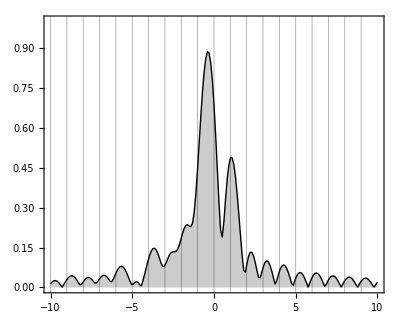

```mathematica
ppM=ListLinePlot[ParallelTable[Icmax[1,.5,.1,-1,.05,-.1,Φ],{Φ,-10,10,.101}],DataRange->{-10,10},PlotStyle->{Thick,Lighter[Black,.0]},Frame->True,PlotRange->{0,1},LabelStyle->{Black,FontSize->18},AspectRatio->.8,GridLines->{Table[{i,Black},{i,-40,40}],None},Filling->Bottom]
```

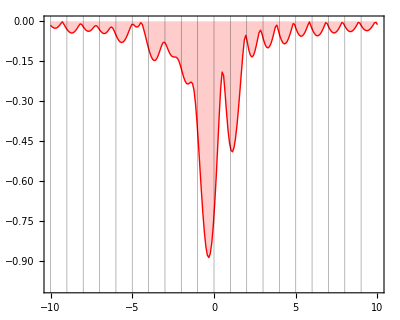

```mathematica
ppm=ListLinePlot[ParallelTable[Icmin[1,.5,.1,-1,.05,-.1,Φ],{Φ,-10,10,.0901}],DataRange->{-10,10},PlotStyle->{Thick,Lighter[Red,.0]},Frame->True,PlotRange->{-1,0},LabelStyle->{Black,FontSize->18},AspectRatio->.8,GridLines->{Table[{i,Black},{i,-40,40}],None},Filling->Top]
```

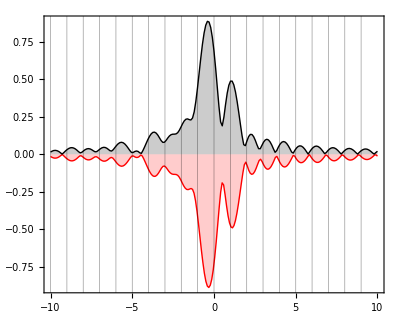

```mathematica
Show[ppm,ppM,PlotRange->All]
```